# Feature Space

Data features exploration

Pavlo Apisov, Jun. 27,  2018

In the world of machine learning, dimensionality is a serious thing to consider because in some cases the more dimensions in data the harder it could be to learn and generalize.

We can use features space to control number of dimensions and use data in more meaningful ways.

## Meaningful data

Adding a conceptual meaning to data is the most important quality of a feature space representation.

Exploring a feature space of your data could help to find variables where similar data points closer to each other.

Let’s draw 4 differently colored figures and treat them as our input  data:

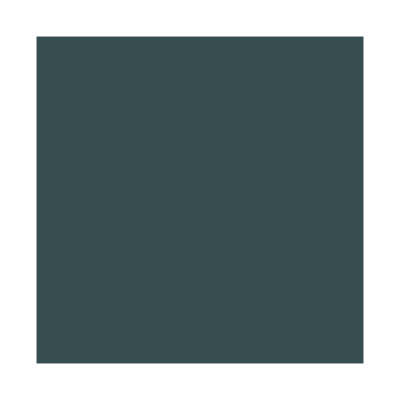
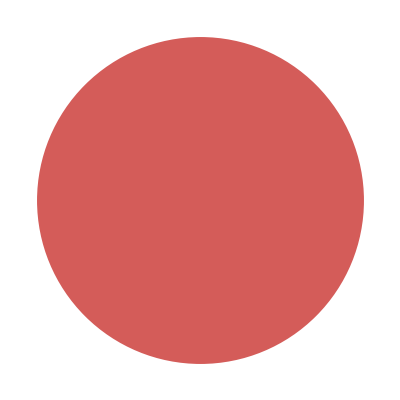
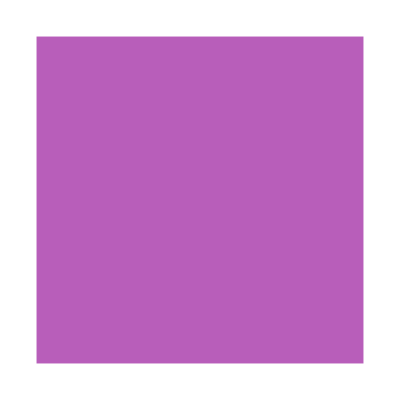
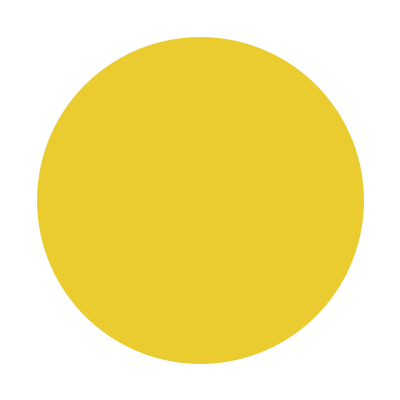

```mathematica
figures = {Graphics[{RGBColor[0.22, 0.3, 0.31],Rectangle[]}], Graphics[{RGBColor[0.83, 0.36, 0.35],Disk[]}], Graphics[{RGBColor[0.72, 0.37, 0.73],Rectangle[]}],Graphics[{RGBColor[0.92, 0.8, 0.19],Disk[]}]}
```

As an example, in the pixel space, there is no similarity between any two figures above.

If we plot the pixel space of the data we see a random layout.

```mathematica
FeatureSpacePlot[figures, ImageSize->{120,120}]
```

-Graphics-

Nevertheless, if we try to find new features you would want rectangles to be closer to each other in the new feature space than to any of circles.

To do so, we could use shape of figures as a new feature.

In our case we use edge detection to construct new feature space representation

```mathematica
FeatureSpacePlot[figures, ImageSize->{120,120}, FeatureExtractor->EdgeDetect]
```

-Graphics-

The way how figures represented in the new feature space is much more reasonable than just the pixel space.

To recapitulate, feature space shows the connections within your data with respect to your task.

I.e for image classification problem, you find features that images with similar meaning(pictures of cat, for example) are closer in that space.

## Exploring handwritten digits

To extend the basic example let’s explore classification of handwritten digits in MNIST dataset.

For the purpose of consistency, we will follow the same steps as in the basic example.

First, show input data(150 random MNIST digits):

```mathematica
digits=Keys[RandomSample[ResourceData["MNIST"],150]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Comparing to the basic example we can find visual similarity in pixel space of digits

We use the same feature plot that extract image data(pixels) by default:

```mathematica
FeatureSpacePlot[digits]
```

-Graphics-

As you can notice, even without any specific feature extraction the data is grouped almost properly.

Although, the numbers 3, 5 and 8 are too close to each other because they are visually similar and to solve this problem we need a proper feature extractor.

Our new feature extractor is a pretrained on MNIST data model:

```mathematica
FeatureSpacePlot[digits, FeatureExtractor->NetTake[NetModel["LeNet Trained on MNIST Data"],9]]
```

-Graphics-

In the consequence, it’s easy to see now how a correct feature extractor plays a big role in feature space.

As a result, the new feature space has more separated groups of all numbers and most important we’ve solved the problem with the numbers 3, 5 and 8 being in one cluster.

## Cats and Dogs classification

Now let’s take a look at a dataset where pixel space is completely irrelevant.

Import images of lovely pets:

```mathematica
SetDirectory[NotebookDirectory[]];
pets = Import["EssayData", "*.jpg"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

This example is similar to the basic example to such extent that observable image data can’t say any useful information so we need a specific feature space to make sensible classifications.

Plot pixel space of images:

```mathematica
FeatureSpacePlot[pets, LabelingSize->90, ImageSize->{500, 500}]
```

-Graphics-

As expected the data is “randomly” spread out over the pixel space. We will do the same operation as in the previous example - using a pretrained model that was taught to detect objects in image.

Plot the pets in more appropriate feature space:

```mathematica
FeatureSpacePlot[pets, LabelingSize->90, ImageSize->{500, 500}, FeatureExtractor->NetTake[NetModel["Wolfram ImageIdentify Net V1"],22]]
```

-Graphics-

Thanks to “Wolfram ImageIdentify Net V1” model we have nicely grouped pets. Well, there is one mistake but this is likely because of a small dataset.

To sum up, feature space is great tool to explore data and find needed representation with respect to your task.

## Further explorations

At this point you might realize how feature space is important and helpful in the matter of understanding data and adding more meaning to it.

What would be useful to study next is a latent space representation. Our basic example(the first one) somewhat explains the core idea behind a latent space but imagine that color and shape are represented with numbers.

Representing figure as a list of numbers:

```mathematica
Graphics[{RGBColor[0.22, 0.3, 0.31],Rectangle[]}, ImageSize->{50,50}] -> {0.22,0.3, 0.31, 50,50}
```

-Graphics-→{0.22,0.3,0.31,50,50}

In this case, the correlation as a shape could be not so clear and special methods have to be applied to find it.

One of possibilities to explore a latent space is Autoencoder. It’s a special type if neural network that reads input data, encode(compress) it into latent space vectors and decode it to a space similar to input data.

## Author contact information

Email: apisovp@gmail.com

Twitter: apisov_pavlo

GitHub: apisov